```mathematica
sigma = 40;
mu = 600;
P[lambda_] := 1/ Sqrt[2 Pi sigma^2] Exp[-(lambda  - mu)^2 / (2 sigma^2)];
```

```mathematica
xbar[lambda_]:=1.065 Exp[-1/2 ((lambda-595.8)/33.33)^2]+0.366 Exp[-1/2 ((lambda-446.8)/19.44)^2];

ybar[lambda_]:=1.014 Exp[-1/2 ((Log[lambda]-Log[556.3])/0.075)^2];

zbar[lambda_]:=1.839 Exp[-1/2 ((Log[lambda]-Log[449.8])/0.051)^2];
```

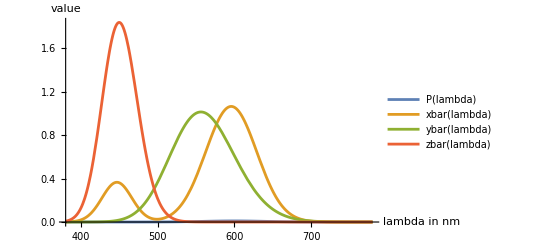

```mathematica
Plot[{P[lambda],xbar[lambda],ybar[lambda],zbar[lambda]},{lambda,380,780},PlotLegends->{"P(lambda)","xbar(lambda)","ybar(lambda)","zbar(lambda)"},AxesLabel->{"lambda in nm","value"},PlotRange->All]
```

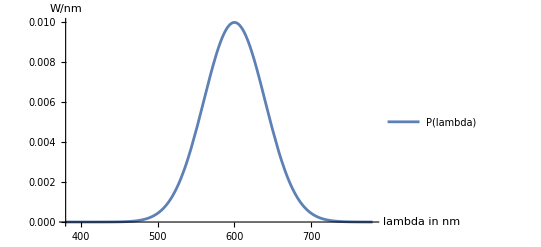

```mathematica
Plot[P[lambda],{lambda,380,780},PlotLegends->{"P(lambda)"},AxesLabel->{"lambda in nm","W/nm"},PlotRange->All]
```

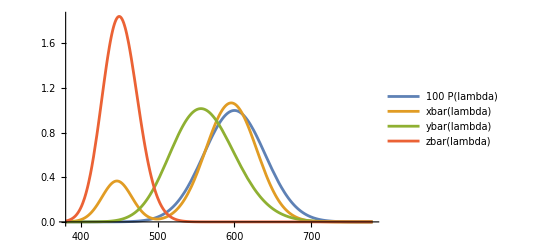

```mathematica
Plot[{100 P[lambda],xbar[lambda],ybar[lambda],zbar[lambda]},{lambda,380,780},PlotLegends->{"100 P(lambda)","xbar(lambda)","ybar(lambda)","zbar(lambda)"},PlotRange->All]
```